# Fermion Lattice Spectral Function EOMs

```mathematica
SetDirectory["/home/steffen/working/calculations/mathematica/Fermions Lattice/data"];
```

```mathematica
$Assumptions={1>u>0,L>0,B>0};
```

```mathematica
L=1;
```

```mathematica
SetOptions[Plot,PlotRange->Full,PlotStyle->Evaluate[Directive[#,Thickness[.005]]&/@{Blue,Red}],FrameStyle->Thickness[.005],FrameLabel->{"x","y"},PlotLabel->"Caption",Frame->True,Axes->False];
SetOptions[ListLinePlot,PlotRange->Full,PlotStyle->Evaluate[Directive[#,Thickness[.005]]&/@{Blue,Red}],FrameStyle->Thickness[.005],FrameLabel->{"x","y"},PlotLabel->"Caption",Frame->True,Axes->False];
SetOptions[Plot3D,PlotRange->{Automatic,Automatic,{0,20}}];
```

## Equations of motion for 0^th order

### Generate 5d Clifford algebra for SO(4,1)

```mathematica
pm[m_]:=PauliMatrix[m]
im[d_]:=IdentityMatrix[d]
η[d_]:=Normal[SparseArray[{{1,1}->-1,{i_,i_}->1},{d,d},0]]
MatrixForm[#]&/@({gamma0,gamma1}={ⅈ pm[2],pm[1]});
MatrixForm[#]&/@({Gamma0,Gamma1,Gamma2,Gamma3}=(KroneckerProduct[#[[1]],#[[2]]])&/@{{gamma0,-pm[3]},{gamma1,-pm[3]},{im[2],pm[1]},{im[2],pm[2]}});
MatrixForm[#]&/@(γ={Gamma0,Gamma1,Gamma2,Gamma3,-ⅈ Dot@@{Gamma0,Gamma1,Gamma2,Gamma3}})
Union[Flatten[Table[γ[[m]].γ[[n]]+γ[[n]].γ[[m]]==2im[4]η[5][[m,n]],{m,5},{n,5}]]]
```

{(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)}

{True}

### Define 4d/4component spinor projectors

```mathematica
Πp=1/2(im[4]+γ[[5]]);
Πm=1/2(im[4]-γ[[5]]);
Π1=1/2(im[4]+γ[[1]].γ[[2]].γ[[5]]);
Π2=1/2(im[4]-γ[[1]].γ[[2]].γ[[5]]);
MatrixForm[#]&/@{Πp,Πm,Π1,Π2}
```

{(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1),(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)}

### Check initial orthogonal basis

```mathematica
γt2=KroneckerProduct[im[2],γ[[1]]];
eeb={{1,-1,1,-1,1,-1,1,-1},{1,-1,-1,1,1,-1,1,-1},{1,-1,1,-1,-1,1,1,-1},{1,-1,1,-1,1,-1,-1,1}};
MatrixForm[Table[eeb[[i]].γt2.eeb[[j]],{i,4},{j,4}]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
MatrixForm[γt=Table[γt2[[i,j]],{i,{1,3,5,7}},{j,{1,3,5,7}}]]
```

(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0)

### Read in EOMs from external file

```mathematica
eqψ0[m_,ω_,kz_]=ReadList["EOM0th.dat"][[1]];
```

## Asymptotics near the horizon u_H=1 up to 3^rd order α<0

```mathematica
hord=3;
Table[α[i]=-(ⅈ ω)/4-1/4,{i,8}];
asymptoticψ=ReadList["AsymptoticH0th6.dat"][[1]];
Table[a[j,i]=(asymptoticψ[[i+1,j]]/.{Cψ[3]->Cψ1,Cψ[4]->Cψ2,Cψ[7]->Cψ3,Cψ[8]->Cψ4}),{i,0,2hord},{j,8}];
```

```mathematica
ψH[u_,m_,ω_,kz_,Cψ1_,Cψ2_,Cψ3_,Cψ4_]=Table[(u-1)^α[j] Sum[a[j,i](u-1)^(i/2),{i,0,2hord}],{j,8}];
ψH[u,m,ω,kz,Cψ1,Cψ2,Cψ3,Cψ4];
```

```mathematica
bord=4;
Table[β[i]=2+L m,{i,{1,4,5,8}}];
Table[β[i]=2-L m,{i,{2,3,6,7}}];
asymptoticψ=ReadList["AsymptoticB0th4.dat"][[1]];
Table[b[j,i]=(asymptoticψ[[i+1,j]]/.Cp[i_]->CBψ[i]),{i,0,bord},{j,8}];
```

```mathematica
ψB[u_,m_,ω_,kz_]=Table[u^β[j] Sum[b[j,i] u^i,{i,0,bord}],{j,8}];
ψB[u,m,ω,kz];
```

## Integration to boundary u_B = 0

```mathematica
IntegrateEOMsψ[eom_,ψ_,ψH_,m_,ω_,kz_,Cψ_,init_,end_]:=
Module[{iend,InitialConditionψ,eomψ,eomψ2,solution},
eomψ=eom[m,ω,kz];
iend=Length[eomψ];
eomψ2=Table[eomψ[[i]]==0,{i,iend}];
InitialConditionψ=Table[ψ[[i]]==ψH[init,m,ω,kz,Cψ[[1]],Cψ[[2]],Cψ[[3]],Cψ[[4]]][[i]],{i,iend}]/.u->init;
solution=NDSolve[Flatten[{eomψ2,InitialConditionψ}],ψ,{u,end,init},MaxSteps->∞,Method->"StiffnessSwitching",PrecisionGoal->12,AccuracyGoal->12][[1]];
ψ/.solution
]
```

```mathematica
IntegrateToBoundariesψ[eom_,ψ_,ψH_,m_,ω_,kz_,Cψ_,init_,end_]:=
Module[{iend,InitialConditionψ,eomψ,eomψ2,solution},
eomψ=eom[m,ω,kz];
iend=Length[eomψ];
eomψ2=Table[eomψ[[i]]==0,{i,iend}];
InitialConditionψ=Table[ψ[[i]]==ψH[init,m,ω,kz,Cψ[[1]],Cψ[[2]],Cψ[[3]],Cψ[[4]]][[i]],{i,iend}]/.u->init;
solution=NDSolve[Flatten[{eomψ2,InitialConditionψ}],ψ,{u,end,init},MaxSteps->∞,Method->"StiffnessSwitching",PrecisionGoal->12,AccuracyGoal->12][[1]];
ψ/.solution/.u->end
]
```

## Determine optimal values for uinit and uend

```mathematica
Clear[m,ω,kz]
```

```mathematica
uinit=1-10^-9;
uend=10^-4;
```

```mathematica
ω=.5;
kz=1.2;
Spinψ=Table[ψ[i][u],{i,8}];
```

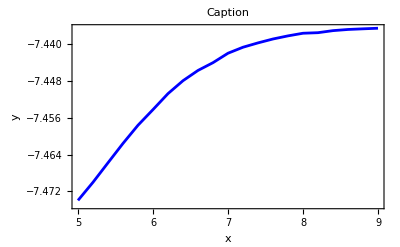
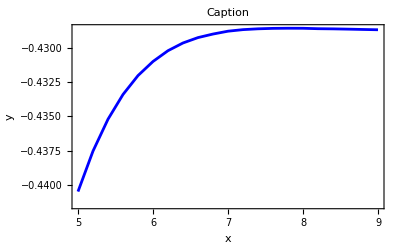
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
m=0;
sol=Table[{i,uend^-2 IntegrateToBoundariesψ[eqψ0,Spinψ,ψH,m,ω,kz,{1,1,1,1},1-10^-i,uend][[#[[2]]]]},{i,5,9,.2}]&/@{{1,1},{0,2},{0,3},{1,4},{1,5},{0,6},{0,7},{1,8}};
Table[ListLinePlot[Re[sol[[j]]]],{j,1,8}]
```

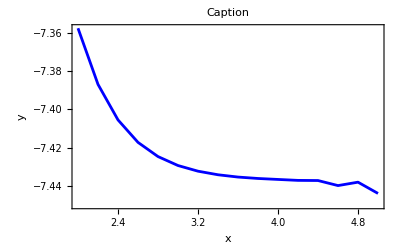
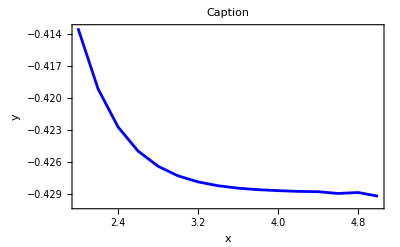
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sol=Table[{i,(10^-i)^-2 IntegrateToBoundariesψ[eqψ0,Spinψ,ψH,m,ω,kz,{1,1,1,1},uinit,10^-i][[#[[2]]]]},{i,2,5,.2}]&/@{{1,1},{0,2},{0,3},{1,4},{1,5},{0,6},{0,7},{1,8}};
Table[ListLinePlot[Re[sol[[j]]]],{j,1,8}]
```

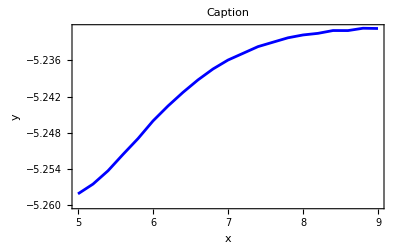
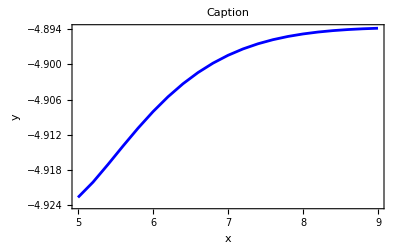
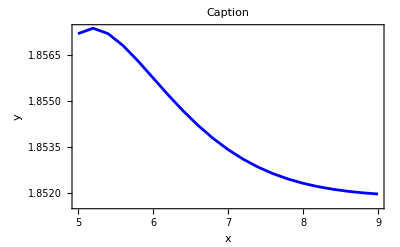
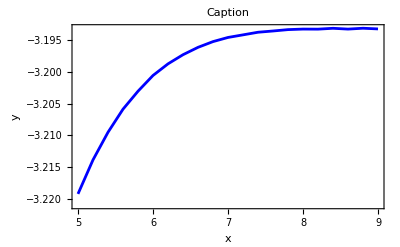
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
m=1;
sol=Table[{i,uend^(-(2-(L m-#[[1]])))IntegrateToBoundariesψ[eqψ0,Spinψ,ψH,m,ω,kz,{1,1,1,1},1-10^-i,uend][[#[[2]]]]},{i,5,9,.2}]&/@{{1,1},{0,2},{0,3},{1,4},{1,5},{0,6},{0,7},{1,8}};
Table[ListLinePlot[Re[sol[[j]]]],{j,1,8}]
```

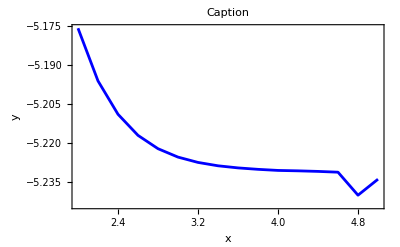
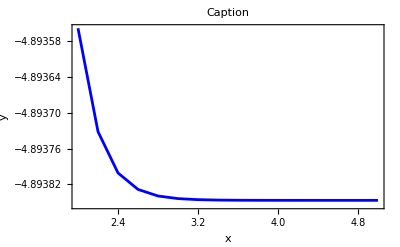
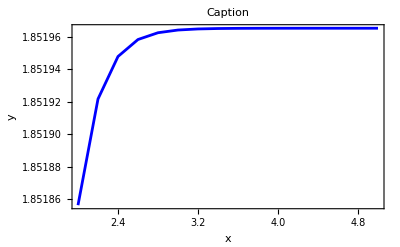
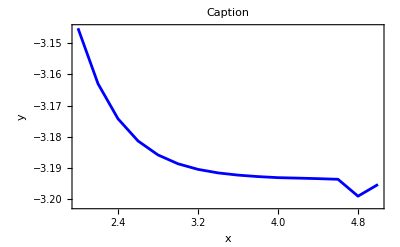
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sol=Table[{i,(10^-i)^(-(2-(L m-#[[1]])))IntegrateToBoundariesψ[eqψ0,Spinψ,ψH,m,ω,kz,{1,1,1,1},uinit,10^-i][[#[[2]]]]},{i,2,5,.2}]&/@{{1,1},{0,2},{0,3},{1,4},{1,5},{0,6},{0,7},{1,8}};
Table[ListLinePlot[Re[sol[[j]]]],{j,1,8}]
```

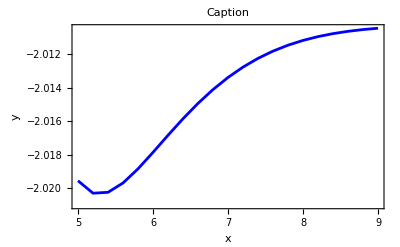
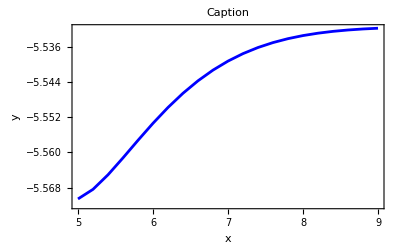
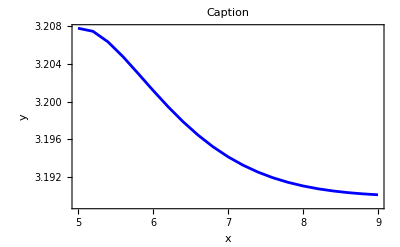
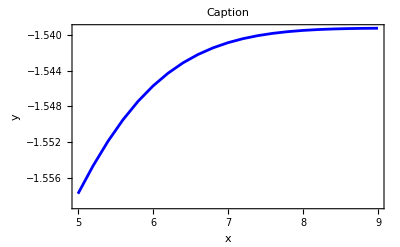
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
m=2;
sol=Table[{i,uend^(-(2-(L m-#[[1]])))IntegrateToBoundariesψ[eqψ0,Spinψ,ψH,m,ω,kz,{1,1,1,1},1-10^-i,uend][[#[[2]]]]},{i,5,9,.2}]&/@{{1,1},{0,2},{0,3},{1,4},{1,5},{0,6},{0,7},{1,8}};
Table[ListLinePlot[Re[sol[[j]]]],{j,1,8}]
```

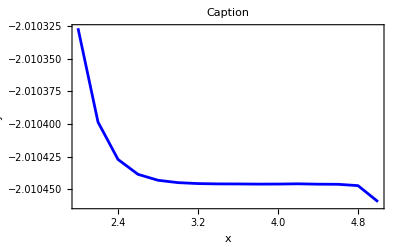
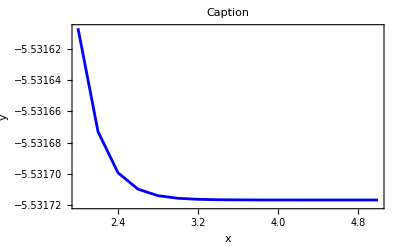
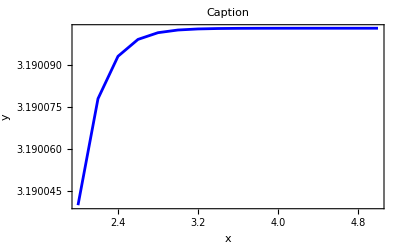
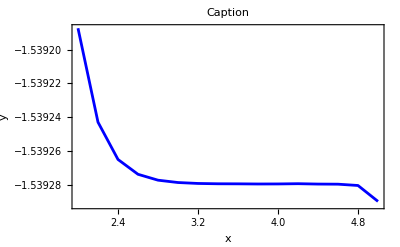
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sol=Table[{i,(10^-i)^(-(2-(L m-#[[1]])))IntegrateToBoundariesψ[eqψ0,Spinψ,ψH,m,ω,kz,{1,1,1,1},uinit,10^-i][[#[[2]]]]},{i,2,5,.2}]&/@{{1,1},{0,2},{0,3},{1,4},{1,5},{0,6},{0,7},{1,8}};
Table[ListLinePlot[Re[sol[[j]]]],{j,1,8}]
```

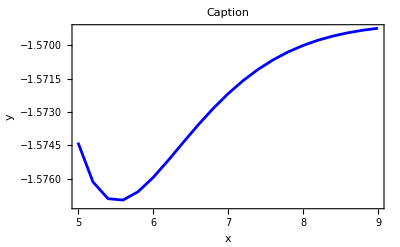
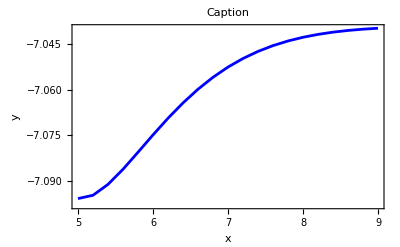
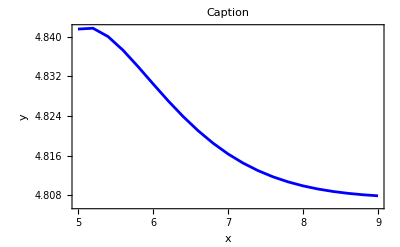
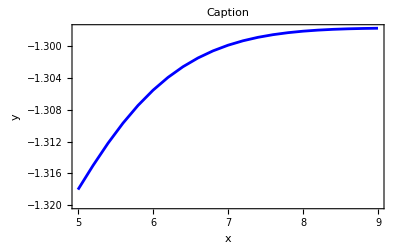
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
m=3;
sol=Table[{i,uend^(-(2-(L m-#[[1]])))IntegrateToBoundariesψ[eqψ0,Spinψ,ψH,m,ω,kz,{1,1,1,1},1-10^-i,uend][[#[[2]]]]},{i,5,9,.2}]&/@{{1,1},{0,2},{0,3},{1,4},{1,5},{0,6},{0,7},{1,8}};
Table[ListLinePlot[Re[sol[[j]]]],{j,1,8}]
```

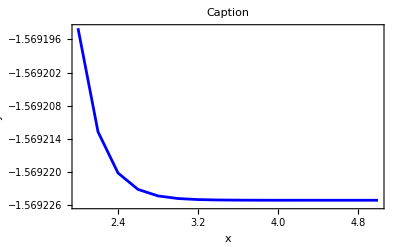
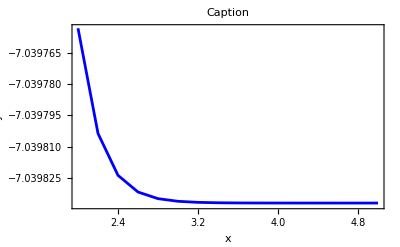
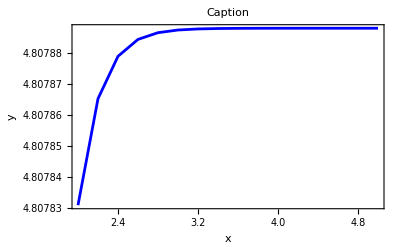
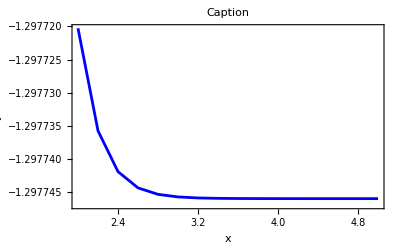
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sol=Table[{i,(10^-i)^(-(2-(L m-#[[1]])))IntegrateToBoundariesψ[eqψ0,Spinψ,ψH,m,ω,kz,{1,1,1,1},uinit,10^-i][[#[[2]]]]},{i,2,5,.2}]&/@{{1,1},{0,2},{0,3},{1,4},{1,5},{0,6},{0,7},{1,8}};
Table[ListLinePlot[Re[sol[[j]]]],{j,1,8}]
```

### Compare with horizon and boundary asymptotic

```mathematica
m=0;
ω=.5;
kz=1.2;
```

```mathematica
solN[uu_]=(IntegrateEOMsψ[eqψ0,Spinψ,ψH,m,ω,kz,{1,1,1,1},uinit,uend]/.u->uu);
```

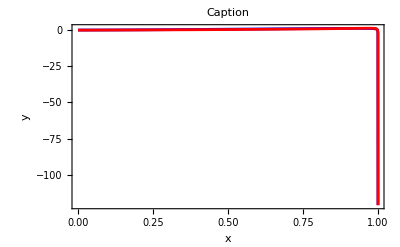

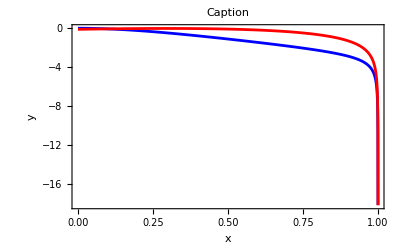

```mathematica
Plot[{Im[solN[u][[2]]],Im[ψH[u,m,ω,kz,1,1,1,1][[2]]]},{u,uinit,uend}]
Plot[{Re[solN[u][[2]]],Re[ψH[u,m,ω,kz,1,1,1,1][[2]]]},{u,uinit,uend}]
```

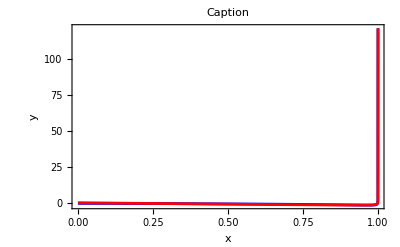
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Plot[{Im[solN[u][[i]]],Im[ψH[u,m,ω,kz,1,1,1,1][[i]]]},{u,uinit,uend}],{i,8}]
```

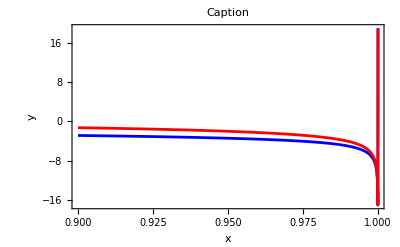
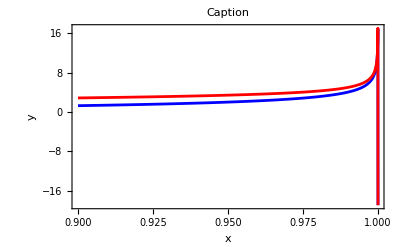
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Plot[{Re[solN[u][[i]]],Re[ψH[u,m,ω,kz,1,1,1,1][[i]]]},{u,uinit,.9}],{i,8}]
```

```mathematica
m=1;
ω=.5;
kz=1.2;
```

```mathematica
solN[uu_]=(IntegrateEOMsψ[eqψ0,Spinψ,ψH,m,ω,kz,{1,1,1,1},uinit,uend]/.u->uu);
```

```mathematica
ψH[.5,m,ω,kz,1,1,1,1][[1]]
```

-0.888717+0.610948 ⅈ

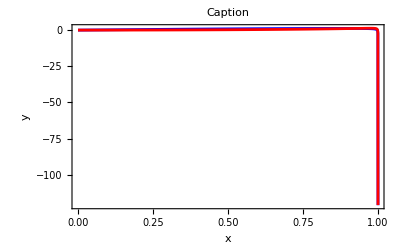

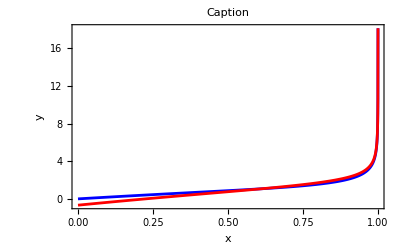

```mathematica
Plot[{Im[solN[u][[2]]],Im[ψH[u,m,ω,kz,1,1,1,1][[2]]]},{u,uinit,uend}]
Plot[{Re[solN[u][[3]]],Re[ψH[u,m,ω,kz,1,1,1,1][[3]]]},{u,uinit,uend}]
```

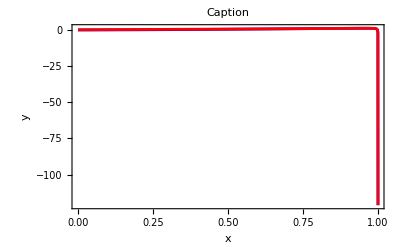
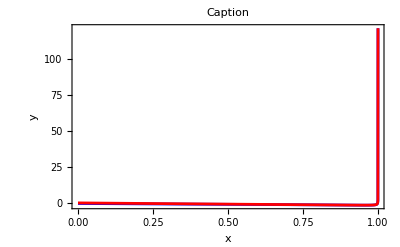
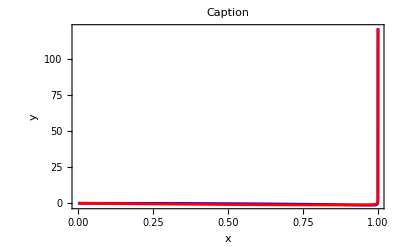
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Plot[{Im[solN[u][[i]]],Im[ψH[u,m,ω,kz,1,1,1,1][[i]]]},{u,uinit,uend}],{i,8}]
```

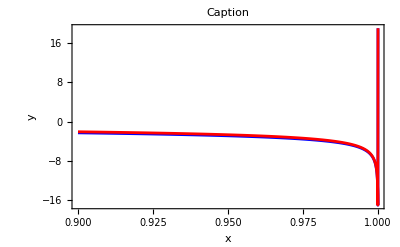
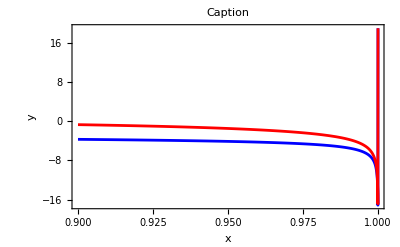
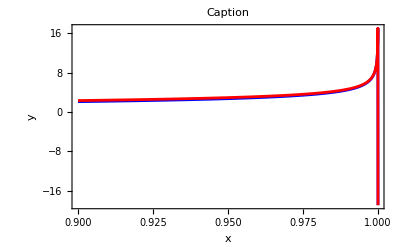
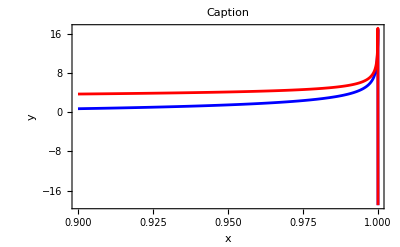
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Plot[{Re[solN[u][[i]]],Re[ψH[u,m,ω,kz,1,1,1,1][[i]]]},{u,uinit,.9}],{i,8}]
```

## Construct projectors at u_B=0 and calculate the Green’s function

### Green’s function, spectral function and spectral measure for m=0

```mathematica
GreensFunctionm0[ω_,kz_,init_,end_]:=
Module[{Spinψ,Cψ,solution1,solution2,solution3,solution4,Πpbdry,Πmbdry},
Spinψ=Table[ψ[i][u],{i,8}];
Cψ={{1,1,1,1},{1,-1,1,1},{1,1,-1,1},{1,1,1,-1}};
solution1=IntegrateToBoundariesψ[eqψ0,Spinψ,ψH,0,ω,kz,Cψ[[1]],init,end];
solution2=IntegrateToBoundariesψ[eqψ0,Spinψ,ψH,0,ω,kz,Cψ[[2]],init,end];
solution3=IntegrateToBoundariesψ[eqψ0,Spinψ,ψH,0,ω,kz,Cψ[[3]],init,end];
solution4=IntegrateToBoundariesψ[eqψ0,Spinψ,ψH,0,ω,kz,Cψ[[4]],init,end];
Πpbdry=Transpose[{{solution1[[1]],solution1[[4]],solution1[[5]],solution1[[8]]},{solution2[[1]],solution2[[4]],solution2[[5]],solution2[[8]]},{solution3[[1]],solution3[[4]],solution3[[5]],solution3[[8]]},{solution4[[1]],solution4[[4]],solution4[[5]],solution4[[8]]}}];
Πmbdry=Transpose[{{solution1[[2]],solution1[[3]],solution1[[6]],solution1[[7]]},{solution2[[2]],solution2[[3]],solution2[[6]],solution2[[7]]},{solution3[[2]],solution3[[3]],solution3[[6]],solution3[[7]]},{solution4[[2]],solution4[[3]],solution4[[6]],solution4[[7]]}}];
ⅈ Πpbdry.Inverse[Πmbdry].γ[[3]]
(*-ⅈ Πpbdry.Inverse[Πmbdry].γt*)
]
```

```mathematica
SpectralFunctionm0[ω_,kz_,init_,end_]:=
Module[{Gf},
Gf=GreensFunctionm0[ω,kz,init,end];
ⅈ(Gf-ConjugateTranspose[Gf])
]
```

```mathematica
SpectralMeasurem0[ω_,kz_,init_,end_]:=
Module[{Rf},
Rf=SpectralFunctionm0[ω,kz,init,end];
Tr[Rf]
]
```

## Determine pole structure of Green’s function, spectral function and spectral measure

```mathematica
uinit=1-10^-9;
uend=10^-4;
```

```mathematica
MatrixForm[GreensFunctionm0[.5,.4,uinit,uend]]
```

(-0.314899-0.878841 ⅈ | -0.397473+0.696265 ⅈ | -1.50665×10^-9+3.00788×10^-8 ⅈ | 3.28518×10^-8-4.5603×10^-8 ⅈ
0.397473-0.696265 ⅈ | -0.314899-0.878841 ⅈ | -3.28518×10^-8+4.5603×10^-8 ⅈ | 9.77034×10^-8-3.8153×10^-8 ⅈ
3.28518×10^-8-4.5603×10^-8 ⅈ | 1.50665×10^-9-3.00788×10^-8 ⅈ | -0.314899-0.878841 ⅈ | -0.397473+0.696265 ⅈ
9.77034×10^-8-3.8153×10^-8 ⅈ | 3.28518×10^-8-4.5603×10^-8 ⅈ | 0.397473-0.696265 ⅈ | -0.314899-0.878841 ⅈ)

```mathematica
MatrixForm[SpectralFunctionm0[.5,.4,uinit,uend]]
```

(1.75768+0. ⅈ | 6.82318×10^-8-0.794945 ⅈ | 1.55242×10^-8-3.43585×10^-8 ⅈ | 8.3756×10^-8-6.48516×10^-8 ⅈ
6.82318×10^-8+0.794945 ⅈ | 1.75768+0. ⅈ | -1.55242×10^-8-3.43585×10^-8 ⅈ | 8.3756×10^-8+6.48516×10^-8 ⅈ
1.55242×10^-8+3.43585×10^-8 ⅈ | -1.55242×10^-8+3.43585×10^-8 ⅈ | 1.75768+0. ⅈ | 0.-0.794945 ⅈ
8.3756×10^-8+6.48516×10^-8 ⅈ | 8.3756×10^-8-6.48516×10^-8 ⅈ | 0.+0.794945 ⅈ | 1.75768+0. ⅈ)

```mathematica
MatrixForm[Eigenvalues[SpectralFunctionm0[.5,.4,uinit,uend]]]
```

(2.55263
2.55263
0.962737
0.962736)

```mathematica
Timing[SpectralMeasurem0[.5,.4,uinit,uend]]
```

{0.32002,7.03073+0. ⅈ}

### Check symmetries of spectral function

```mathematica
CheckSymmetries[ω_,kz_,init_,end_]:=
Module[{Rab,Rabωm,Rabkzm,Rabωkzm},
Rab=SpectralFunctionm0[ω,kz,init,end];
Rabωm=SpectralFunctionm0[-ω,kz,init,end];
Rabkzm=SpectralFunctionm0[ω,-kz,init,end];
Rabωkzm=SpectralFunctionm0[-ω,-kz,init,end];
Flatten[Join[{Rabωm[[1,1]]-Rab[[4,4]],Rabωm[[2,2]]-Rab[[3,3]],Rabkzm[[1,1]]-Rab[[2,2]],Rabkzm[[3,3]]-Rab[[4,4]],Rabωkzm[[1,1]]-Rab[[4,4]],Rabωkzm[[2,2]]-Rab[[3,3]]},Table[Rabkzm[[a,b]]-(-1)^(a+b)Conjugate[Rab[[b,a]]],{a,Length[Rab]},{b,Length[Rab]}]]]
]
```

```mathematica
MatrixForm[numericcheck=ParallelTable[Norm[CheckSymmetries[.3,.4,uinit,uend]],{ω,0,2},{kx,0,2},{ky,0,2}]]
```

((6.18999×10^-8
6.18999×10^-8
6.18999×10^-8) | (6.18999×10^-8
6.18999×10^-8
6.18999×10^-8) | (6.18999×10^-8
6.18999×10^-8
6.18999×10^-8)
(6.18999×10^-8
6.18999×10^-8
6.18999×10^-8) | (6.18999×10^-8
6.18999×10^-8
6.18999×10^-8) | (6.18999×10^-8
6.18999×10^-8
6.18999×10^-8)
(6.18999×10^-8
6.18999×10^-8
6.18999×10^-8) | (6.18999×10^-8
6.18999×10^-8
6.18999×10^-8) | (6.18999×10^-8
6.18999×10^-8
6.18999×10^-8))

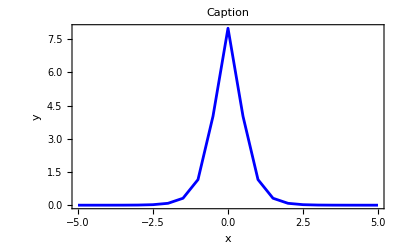

```mathematica
Table[{k,SpectralMeasurem0[0,k,uinit,uend]},{k,-5,5,.5}];
ListLinePlot[Re[%]]
```

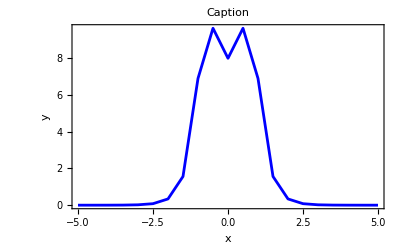

```mathematica
Table[{k,SpectralMeasurem0[1,k,uinit,uend]},{k,-5,5,.5}];
ListLinePlot[Re[%]]
```

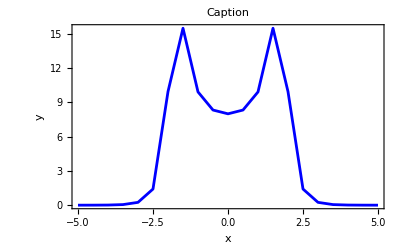

```mathematica
Table[{k,SpectralMeasurem0[2,k,uinit,uend]},{k,-5,5,.5}];
ListLinePlot[Re[%]]
```

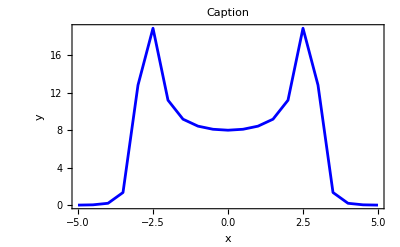

```mathematica
Table[{k,SpectralMeasurem0[3,k,uinit,uend]},{k,-5,5,.5}];
ListLinePlot[Re[%]]
```